```mathematica
$HPLPath="C:\\Program Files\\Wolfram Research\\Mathematica\\11.2\\HPL";$Path=Flatten[{$Path,$HPLPath}];
<<HPL`;
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

-Log[z]

0

1/2 (HPL[{-1,3},z]+HPL[{1,3},z])

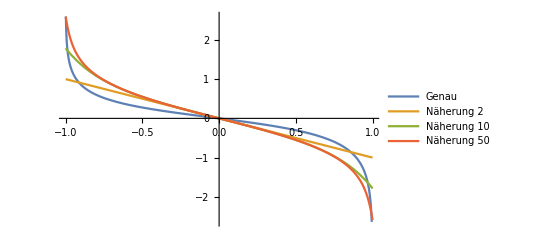

```mathematica
a[z_]=-1/z;
b[z_]=HPL[{3},z]/(z(z+1)(1-z));
A[z_]=Integrate[a[z],z]
c0=0(*=y[0]*)
c[z_]=1/2*(Integrate[HPL[{3},x]/(1-x),{x,0,z}]+Integrate[HPL[{3},x]/(1+x),{x,0,z}])
(*   y[x]=Exp[A[x]]*(Integrate[b[t]*Exp[-A[t]],t]+c0)  ; c0=0 damit xy'[x]=y[x] bei 0≠Inf *)
y[x_]:=y[x]=Exp[A[x]]*(c0+c[x])
pol[i_]:=pol[i]=SeriesCoefficient[Series[HPL[{3},x]/(x(x+1)(x-1)),{x,0,i}],i]
liste[i_]:=liste[i]=Join[liste[i-1],Solve[(i-1)B[i]==pol[i-1]-B[i],B[i]][[1]]]
liste[0]={B[0]->0};
funct[x_,n_]:=funct[x,n]=Sum[B[i]*x^i/.liste[n],{i,0,n}]
Plot[{-y[x],Evaluate[Table[funct[x,k],{k,{2,10,50}}]]},{x,-1,1},PlotLegends->{Genau,"Näherung 2","Näherung 10","Näherung 50"}]
```

```mathematica
ClearAll["Global`*"]
```

ClearAll::wrsym: Symbol HPL is Protected.